## Working with units

Katharine Long, Texas Tech University

Units are helpful for catching mistakes.

## Example: free fall time

The free fall time of an object dropped from height h is:

```mathematica
Subscript[T, fall]=Sqrt[2 h/g]
```

√2 √(h/g)

We can plug in numbers using substitution rules,

```mathematica
Subscript[T, fall]/. {h-> 10, g-> 9.81}
```

1.42784

However, it’s helpful to work with units. That’s done using the Quantity function. The units are given by strings: “Meter”, “Second”, “Kilogram”, etc.

```mathematica
Subscript[T, fall]/. {h-> Quantity[10,"Meter"], g-> Quantity[9.81, "Meter/Second/Second"]}
```

1.42784 s

Mathematica is flexible about how you specify units.

```mathematica
Subscript[T, fall]/. {h-> Quantity[10,"mtr"], g-> Quantity[9.81, "m /sec^2"]}
```

1.42784 s

#### Catching mistakes

Including units is helpful for catching mistakes. Suppose I goofed and wrote T=√(2h/m g) instead of T=√(2h/g).

```mathematica
Subscript[T, doh]=Sqrt[2h/g/m]
```

√2 √(h/(g m))

```mathematica
Subscript[T, doh]/. {h-> 10, g-> 9.81,m->0.1}
```

4.51524

It’s hard to spot the error in a pure number.

```mathematica
Subscript[T, doh]/.  {h-> Quantity[10,"Meter"], g-> Quantity[9.81, "Meter/Second/Second"],m-> Quantity[0.1, "kg"]}
```

4.51524 s/√kg

The units came out wrong: a big flashing red light telling me I’ve made a mistake.

## Example: Rutherford scattering

In the SubstitutionRules document, we worked through an estimate of the scattering angle in Rutherford’s gold foil experiment.

```mathematica
Δv = Subscript[Z, 1] Subscript[Z, 2] e^2/(4 Pi Subscript[ϵ, 0] Subscript[m, α]) Integrate[b/(b^2 + v^2t^2)^(3/2),{t,-Infinity,Infinity},Assumptions->{v>0,b>0}]
```

(e^2 Z_1 Z_2)/(2 π b v ϵ_0 m_α)

We plugged in numbers for the “plum pudding” model

```mathematica
Δθ=180/Pi ArcTan[Δv/v] /.  {b -> 10^-10, e-> 1.602 10^-19,Subscript[Z, 1]->79,Subscript[Z, 2]-> 2,v-> 1.5 10^7, Subscript[ϵ, 0]-> 8.854 10^-12, Subscript[m, α]->6.645 10^-27}
```

0.0279324

It’s easy to make a mistake in typing in all those numbers, and it’s hard to catch any mistakes we might have made in deriving the formula. Units to the rescue.

```mathematica
Δθ=Quantity[180/Pi,"Degree"] ArcTan[Δv/v] /.  {
b ->Quantity[10^-10,"Meter"],
e-> Quantity[1.602 10^-19,"Coulomb"],Subscript[Z, 1]->79,Subscript[Z, 2]-> 2,
v-> Quantity[1.5 10^7, "Meter/Second"],
Subscript[ϵ, 0]->Quantity[8.854 10^-12,"Farad/Meter"],
Subscript[m, α]->Quantity[6.645 10^-27, "Kilogram"]}
```

0.0279324 °

The result is in degrees, as expected.

Following Rutherford, try again with a smaller b, say b=10^-14m:

```mathematica
Δθ=Quantity[180/Pi,"Degree"] ArcTan[Δv/v] /.  {
b ->Quantity[10^-14,"Meter"],
e-> Quantity[1.602 10^-19,"Coulomb"],Subscript[Z, 1]->79,Subscript[Z, 2]-> 2,
v-> Quantity[1.5 10^7, "Meter/Second"],
Subscript[ϵ, 0]->Quantity[8.854 10^-12,"Farad/Meter"],
Subscript[m, α]->Quantity[6.645 10^-27, "Kilogram"]}
```

78.4081 °

## Example: electromagnetic skin depth

An electromagnetic wave cannot penetrate far into a conductor: the varying EM fields cause eddy currents which lose energy because of finite conductivity in the material. In an EM course you’ll derive the “skin depth”, which at low frequencies is δ=√(2/σωμ); here σ is the conductivity, ω is the angular frequency of the EM wave, and μ is the magnetic permeability of the material. Engineers often work with cyclical frequency f rather than angular frequency ω=2π f, so I’ll write the expression in terms of f

```mathematica
δ=Sqrt[2/(σ 2π f μ)]
```

(√(1/(f μ σ)))/(√π)

Skin depth for copper at 1 KHz:

```mathematica
Subscript[δ, Cu]=δ /. {σ->Quantity[5.96 10 ^7, "Siemen/Meter"], f-> Quantity[1000, "Hertz"],
μ-> Quantity[4 Pi 10^-7, "Henry/Meter"]}
```

0.00206156 m/(√Hz √H √S)

Mathematica needs a little more help to convert this to base units.

```mathematica
UnitSimplify[Subscript[δ, Cu]]
```

0.00206156 m

The skin depth is about 2 mm. If you’d like to see the results explicitly in millimeters, that’s easily done with the UnitConvert function

```mathematica
UnitConvert[Subscript[δ, Cu],"Millimeter"]
```

2.06156 mm

You can convert to any crazy length unit you like

```mathematica
{UnitConvert[Subscript[δ, Cu],"Inch"],UnitConvert[Subscript[δ, Cu],"Light Year"],UnitConvert[Subscript[δ, Cu],"Angstrom"]}
```

{0.081164 in,2.17908×10^-19 ly,2.06156×10^7 Å}

You’ll be unable to convert to a unit that isn’t a length:

```mathematica
UnitConvert[Subscript[δ, Cu],"Week"]
```

Quantity::compat: Meters/(√Henries √Hertz √Siemens) and Weeks are incompatible units

$Failed

## Plotting with units

The Plot function is aware of units.

```mathematica
skinDepth[ν_]=UnitSimplify[δ /. {σ->Quantity[5.96 10 ^7, "Siemen/Meter"],f->ν,
μ-> Quantity[4 Pi 10^-7, "Henry/Meter"]}]
```

(√((0.0133519 m^2/s)/ν))/(√π)

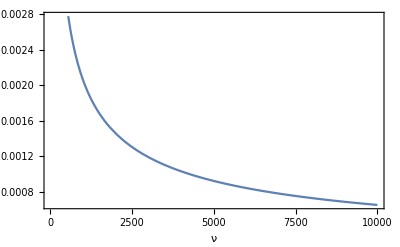

```mathematica
Plot[skinDepth[ν],{ν,Quantity[10,"Hertz"],Quantity[10000,"Hertz"]},FrameLabel->Automatic]
```

Plot will catch incompatible units

```mathematica
Plot[skinDepth[ν],{ν,Quantity[10,"Hertz"],Quantity[10000,"Acres"]},FrameLabel->Automatic]
```

Plot::plld: Endpoints for ν in {ν,10,10000} must have distinct machine-precision numerical values.

Quantity::compat: Acres and Hertz are incompatible units

Plot::plln: Limiting value QuantityMagnitude[$Failed] in {ν,10,QuantityMagnitude[$Failed]} is not a machine-sized real number.

Plot[skinDepth(ν),{ν,10 Hz,10000 acres},FrameLabel→Automatic]